# Econ 382 Homework

## Assignment 1: 17.1, 17.3, 17.6

### 17.1

```mathematica
U [c1_,c2_]:= Log[c1]+1/(1+δ)*Log[c2];
u = U[c1,c2];
```

```mathematica
W[c1_,c2_,r_]=c1+c2/(r+1);
we = W[c1,c2,r];
Clear[w];
w-we
```

-c1-c2/(r+1)+w

```mathematica
L[u_]=u+λ*(w-we);
l = L[u]
```

λ (-c1-c2/(r+1)+w)+log(c1)+(log(c2))/(δ+1)

```mathematica
D[l,c1]
D[l,c2]
D[l,λ]
```

1/c1-λ

1/(c2 (δ+1))-λ/(r+1)

-c1-c2/(r+1)+w

```mathematica
Solve[D[l,c1]==0 && D[l,c2]==0 &&D[l,λ]==0,{c1,c2,λ}]
```

{{c1→(δ w+w)/(δ+2),c2→(r w+w)/(δ+2),λ→(δ+2)/((δ+1) w)}}

### 17.3

```mathematica
Exp[2 √0-.15*0]
```

1.

```mathematica
Limit[2*√x-.15*x,x-> ∞]
```

-∞

```mathematica
D[Exp[2 √x-.15*x],x]
```

ⅇ^(2 √x-0.15 x) (1/(√x)-0.15)

```mathematica
D[Exp[-r*t],t]
```

r (-ⅇ^(-r t))

```mathematica
(1/.2)^2
```

25.

### 17.6

```mathematica
Sum[2000/(1+.1)^i,{i,0,3}]
```

6973.7

```mathematica
Sum[400/(1+.1)^i,{i,0,34}]
```

4243.43

```mathematica
400/1.1^35
```

14.2336

## Assignment 4: 14.6, 14.7, 14.8

### 14.6

```mathematica
55-45/2
```

65/2

```mathematica
35-25/2
```

45/2

```mathematica
65/2*45/2+25*45/2- (25+45/2)*5//N
```

1056.25

```mathematica
55-65/2
```

45/2

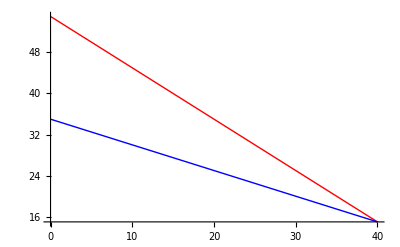

```mathematica
Plot[{55-x,35-x/2},{x,0,40},PlotStyle-> {Red,Blue}]
```

```mathematica
125/3
```

125/3

```mathematica
N[125/2]
```

62.5

```mathematica
125/3-125/(2*3)
```

125/6

```mathematica
N[125/6]
```

20.8333

```mathematica
N[(125/2)*125/6-(125/2)*5]
```

989.583

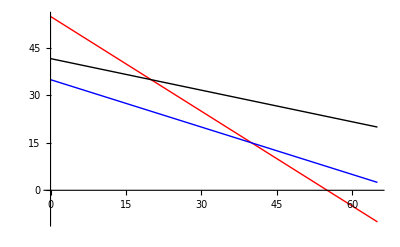

```mathematica
Plot[{55-x,35-x/2,125/3-x/3},{x,0,65},PlotStyle-> {Red,Blue,Black}]
```

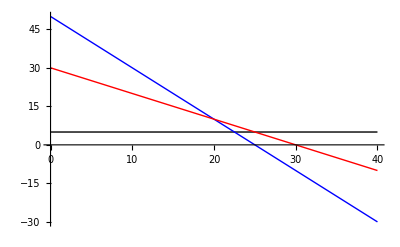

```mathematica
Plot[{5, 55-2x-5,35-x-5},{x,0,40},PlotStyle->{Black, Blue,Red}]
```

```mathematica
x/.Solve[55-2x-5==5,x][[1]]
```

45/2

```mathematica
Manipulate
```

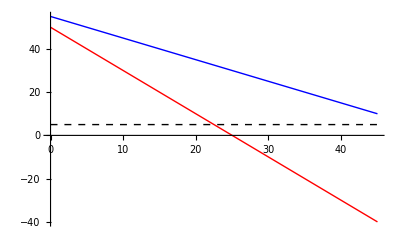

```mathematica
Plot[{55-q,55-2q-5,5},{q,0,45},PlotStyle->{{Blue,Thick},{Red,Thick},{Black,Dashed}},GridLines->{{x/.Solve[55-2x-5==5,x][[1]]},{}}]
```

```mathematica
Manipulate[Plot[{maxd-const*q,maxd - const*2*q- ac, mc},{q,0,(q/.Solve[maxd-const*q==0,q][[1]])},
GridLines->{{q/.Solve[maxd-2*const*q-ac==mc,q][[1]]},
{maxd-const*(q/.Solve[maxd-2*const*q-ac==mc,q][[1]])}},
PlotRange->{0,maxd+maxd/15}],
{{maxd,55},5,200},
{{const,1},.1,10},
{{ac,5},1,50},
{{mc,5},0,150}]
```

```mathematica
Manipulate[Show[Graphics[{ Blue,Opacity->0.15,Polygon[{{0,maxd},
{q/.Solve[maxd-2*const*q-ac==mc,q][[1]],maxd-const*(q/.Solve[maxd-2*const*q-ac==mc,q][[1]])}
,{0,maxd-const*(q/.Solve[maxd-2*const*q-ac==mc,q][[1]])}}],Red,Opacity->0.2}],
Plot[{maxd-const*q,maxd - const*2*q- ac, mc},{q,0,(q/.Solve[maxd-const*q==0,q][[1]])},
GridLines->{{q/.Solve[maxd-2*const*q-ac==mc,q][[1]]},
{maxd-const*(q/.Solve[maxd-2*const*q-ac==mc,q][[1]])}},
PlotRange->{0,maxd+maxd/15}],Axes->True],
{{maxd,55},5,200},
{{const,1},.1,10},
{{ac,5},1,50},
{{mc,5},0,150}]
```

```mathematica
Graphics[{Red,Opacity->0.3,Polygon[{{0,55},{45/2,65/2},{0,65/2}}]}]
```